## Brusselator Model

Reference:
Prigogene L, Lefever R. Symmetry breakign instabilities in dissipative systems. II. J. Chem. Phys 48, 1695-1700 (1968). doi: 10.1063/1.1668896

xCellerator implementation
created: 14 Aug 2005 BES
revised: 15 Oct 2007 BES - verified under Version 6.0
revised: 25 Oct 2009 BES - verified 7.0, add CelleratorML dump

```mathematica
<<xlr8r.m
```

xlr8r 0.74 (13 May 2009) loaded 25 October 2009 at 10:06 GMT-06:60 using Mathematica 7.0 for Linux x86 (64-bit) (February 18, 2009) (Version 7., Release 1) (MathSBML 2.9.0 [8-Oct-2008])
GNU Lesser General Public License (LGPL) Terms Apply.

### Original System

We use lower case letters for the species D and E in the original paper to avoid conflicts with the Mathematica system symbols D (Differentiation) and E (Exponentiation)

```mathematica
stn={
{A->X, k1}, 
{B+X->d+ Y, k2},
{2X+Y-> 3X, k3}, 
 {X-> e, k4}};
```

### revised system

in fact, the species d and e are not important to us because they are "removed" from the (mathematical) system, and we are only interested in the dynamics of the variablers X and Y (we are going to hold A and B constant).

Since we don't care about d and e, and equivalent system is:

```mathematica
stn={
{A->X, k1}, 
{B+X-> Y, k2},
{2X+Y-> 3X, k3}, 
 {X-> ∅, k4}};
```

```mathematica
eqs=interpret[stn, frozen-> {A,B}]
```

{{A'[t]==0,B'[t]==0,X'[t]==k1 A[t]-k4 X[t]-k2 B[t] X[t]+k3 X[t]^2 Y[t],Y'[t]==k2 B[t] X[t]-k3 X[t]^2 Y[t]},{A,B,X,Y}}

```mathematica
ss=steadyState[{{X'[t]==k1 A-k4 X[t]-k2 B X[t]+k3 X[t]^2 Y[t],Y'[t]==k2 B X[t]-k3 X[t]^2 Y[t]},{X[t],Y[t]}},t, {X[t],Y[t]}]
```

{{Y[t]→(B k2 k4)/(A k1 k3),X[t]→(A k1)/k4}}

```mathematica
ss/.{A-> 1, B-> 1, k1-> 1, k2-> 2, k3-> 1, k4-> 1}
```

{{Y[t]→2,X[t]→1}}

Warning:  The following symbols are undefined (and assumed to be equal to one (1)): {k1,k3,k4}

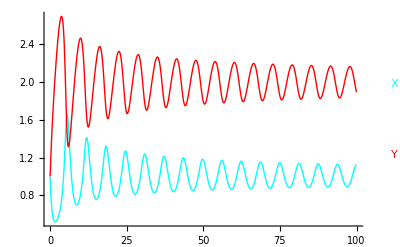

{{A→InterpolatingFunction[{{0.,100.}},<>],B→InterpolatingFunction[{{0.,100.}},<>],X→InterpolatingFunction[{{0.,100.}},<>],Y→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
num=run[eqs,{0,100}, initialConditions-> {A-> 1, B-> 1, X->1, Y->1}, rates-> {k2-> 2}, plot-> True, plotVariables-> {X,Y}]
```

### repeat with original system

```mathematica
stn={
{A->X, k1}, 
{B+X->d+ Y, k2},
{2X+Y-> 3X, k3}, 
 {X-> e, k4}};
```

```mathematica
eqs=interpret[stn, frozen-> {A,B}]
```

{{A'[t]==0,B'[t]==0,d'[t]==k2 B[t] X[t],e'[t]==k4 X[t],X'[t]==k1 A[t]-k4 X[t]-k2 B[t] X[t]+k3 X[t]^2 Y[t],Y'[t]==k2 B[t] X[t]-k3 X[t]^2 Y[t]},{A,B,d,e,X,Y}}

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {d,e}

Warning:  The following symbols are undefined (and assumed to be equal to one (1)): {k1,k3,k4}

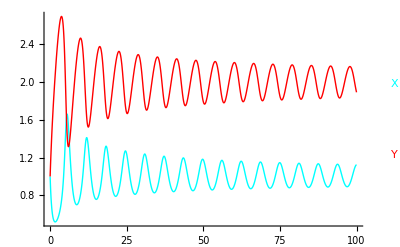

{{A→InterpolatingFunction[{{0.,100.}},<>],B→InterpolatingFunction[{{0.,100.}},<>],d→InterpolatingFunction[{{0.,100.}},<>],e→InterpolatingFunction[{{0.,100.}},<>],X→InterpolatingFunction[{{0.,100.}},<>],Y→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
num=run[eqs,{0,100}, initialConditions-> {A-> 1, B-> 1, X->1, Y->1}, rates-> {k2-> 2}, plot-> True, plotVariables-> {X,Y}]
```

### d and e aren't really very interesting - they just grow & grow

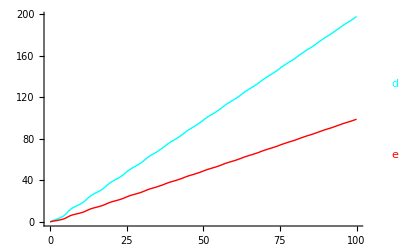

```mathematica
runPlot[num, {d,e}]
```

### Save XML file

```mathematica
<<CelleratorML.m
```

CelleratorML 1.0.5 (19 June 2009) loaded 25 October 2009 at 10:11 GMT-06:60 using Mathematica Version 7.0 for Linux x86 (64-bit) (February 18, 2009) Release 1

```mathematica
SaveModel["Brusselator.xml", stn, "Frozen"-> {A,B}, "InitialConditions"->  {A-> 1, B-> 1, X->1, Y->1, d-> 0, e-> 0}, "Parameters"-> {k2-> 2, k1-> 1, k3-> 1, k4-> 1}, 
"Name"-> "Brusselator"]
```

Brusselator.xml

```mathematica
{model, parms, iv, opts}=GetModel["Brusselator.xml"]
```

Model: Brusselator

CelleratorML Version: 1.0

4 reactions

4 parameters

6 initial values

{{{A→X,k1},{B+X→d+Y,k2},{2 X+Y→3 X,k3},{X→e,k4}},{k2→2,k1→1,k3→1,k4→1},{A→1,B→1,X→1,Y→1,d→0,e→0},{Name→Brusselator,Frozen→{A,B}}}

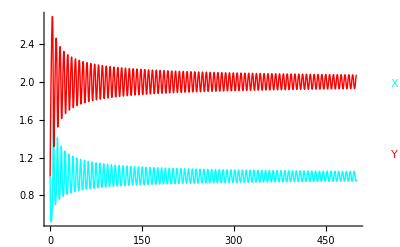

```mathematica
run[model, initialConditions-> iv, rates-> parms, frozen-> ("Frozen"/.opts), timeSpan-> 500]; 
runPlot[%, {X,Y}]
```